```mathematica
$LoadPhi=True;
Needs["HighEnergyPhysics`FeynCalc`"];
```

Loading FeynCalc from /home/bastilo/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/bastilo/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

## Definiciones

```mathematica
dm[mu_]:=DiracMatrix[mu]     (*Matriz de Dirac*)
dm[5]:=DiracMatrix[5]             (*Matriz Chiral*)
ds[p_]:=DiracSlash[p]            (*p^μ Subscript[γ, μ]*)
mt[mu_,nu_]:=MetricTensor[mu,nu]       (*Metrica*)
fv[p_,mu_]:=FourVector[p,mu]           (*4-vector p^μ*)
sp[p_,q_]:=ScalarProduct[p,q]          
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
li[mu_]:=LorentzIndex[mu]
propu[p_,m_]:=ds[p]+m (*Fermion propagator*)
propv[p_,m_]:=ds[p]-m(*Fermion propagator*)
propH[p_]:=I/(p^2-MH^2)(*Higgs propagator*)
propA[p_,mu_,nu_]:=-I*MetricTensor[mu,nu]/p^2 
propZ[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MZ^2)/(p^2-MZ^2) 
propW[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MW^2)/(p^2-MW^2) 
propVC[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MVC^2)/(p^2-MVC^2) 
propV1[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MV1^2)/(p^2-MV1^2) 
propV2[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MV2^2)/(p^2-MV2^2) 
ϵW[p_,mu_]:=FourVector[p,mu]
ϵV[p_,mu_]:=FourVector[p,mu]
ϵZ[p_,mu_]:=FourVector[p,mu]
cteta:=Cos[θ]
steta:=Sin[θ]
```

## FeynmanRules

```mathematica
Zh1h2[p1_,p2_,p3_,mu_,nu_,rho_]:=(e/(2*cw*sw))*(fv[p2,mu]-fv[p3,mu])(*CHECKED*)
ZV1V2[p1_,p2_,p3_,mu_,nu_,rho_]:=-(e/(2*cw*sw))*(fv[p2,mu]*mt[nu,rho]-fv[p3,mu]*mt[nu,rho]-fv[p2,rho]*mt[mu,nu]+fv[p3,nu]*mt[mu,rho]-fv[p1,nu]*mt[mu,rho]+fv[p1,rho]*mt[mu,nu])(*CHECKED*)
Zff[mu_] := -i (g/2*cw)*dm[mu]*(gv-ga*dm[5])
gv=
```

## Amplitude

```mathematica
M=
```

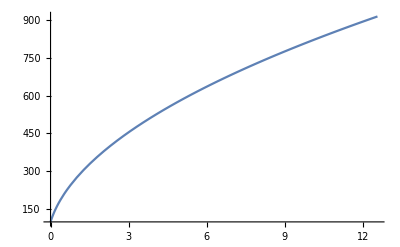

```mathematica
Block[{MV1=100,v=256},Plot[√(λ4*v^2+MV1^2),{λ4,0,4π}]]
```

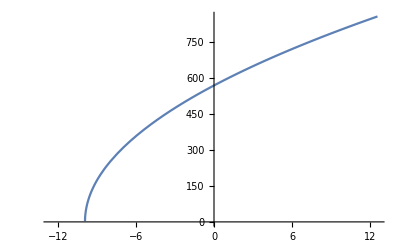

```mathematica
Block[{MV1=100,MV2=800,v=256},Plot[√((λ3*v^2+MV1^2+MV2^2)/2),{λ3,-4π,4π}]]
```